```mathematica
householdsize=PDF[PoissonDistribution[2.51],x]
```

Piecewise[{{(0.0812682 2.51^x)/(x!), x≥0}, {0, True}}]

```mathematica
floorspace=PDF[NormalDistribution[0.01*234.30147,1]]
```

Function[x,(ⅇ^(-1/2 (-2.34301+x)^2))/(√(2 π))]

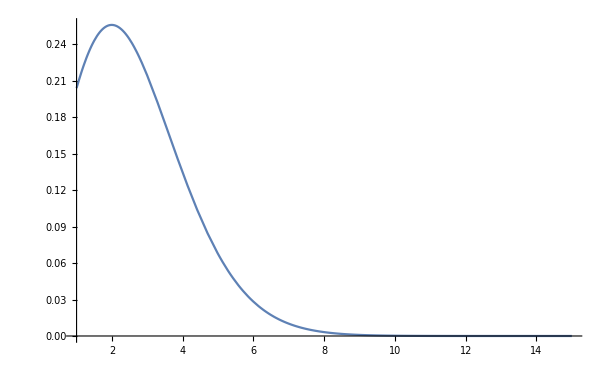

```mathematica
Plot[{householdsize},{x,1,15}]
```

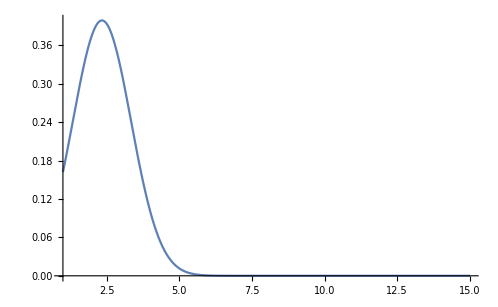

```mathematica
Plot[{floorspace},{x,1,15},PlotRange->All]
```

```mathematica
conv[x_?NumericQ]:=NIntegrate[householdsize[t]*floorspace[x-t],{t,-Infinity,Infinity}]
```